```mathematica
HarmonicNumber[100]-Log[100]//N
```

0.582207

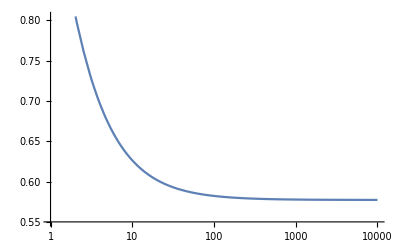

```mathematica
LogLinearPlot[HarmonicNumber[x]-Log[x],{x,1,10^4},PlotRangePadding->Scaled[.02],AxesStyle->Gray,AxesOrigin->{1,0.55}]
```

```mathematica
Integrate[(1-E^(-u))/u,{u,0,1}] - Integrate[E^(-u)/u,{u,1,Infinity}]
Integrate[(1-E^(-u))/u,{u,0,1}] - Integrate[E^(-u)/u,{u,1,Infinity}]//N
```

EulerGamma

0.577216

```mathematica
Integrate[Exp[-u]Log[u],{u,0,Infinity}]
```

-EulerGamma

```mathematica
Integrate[Log[-Log[x]],{x,0,1}]
```

-EulerGamma